## RC Circuit

SquareWave

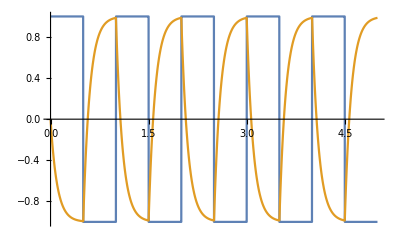

```mathematica
{RVal,CVal}={1.0,0.1};
TMax=5;
V=SquareWave
qSol=NDSolveValue[{q[t]/CVal+RVal q'[t]+V[t]==0,q[0]==0},q,{t,0, TMax}];
Plot[{V[t],qSol[t]/CVal},{t,0, TMax}]
```

TriangleWave

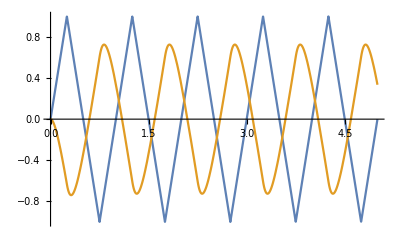

```mathematica
{RVal,CVal}={1.0,0.1};
TMax=5;
V=TriangleWave
qSol=NDSolveValue[{q[t]/CVal+RVal q'[t]+V[t]==0,q[0]==0},q,{t,0, TMax}];
Plot[{V[t],qSol[t]/CVal},{t,0, TMax}]
```

SawtoothWave

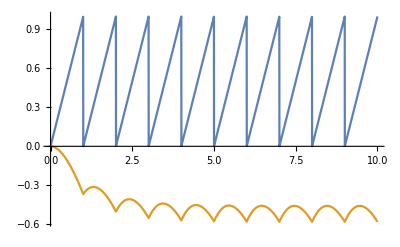

```mathematica
{RVal,CVal}={1.0,1};
TMax=10;
V=SawtoothWave
qSol=NDSolveValue[{q[t]/CVal+RVal q'[t]+V[t]==0,q[0]==0},q,{t,0, TMax}];
Plot[{V[t],qSol[t]/CVal},{t,0, TMax}]
```

Sin

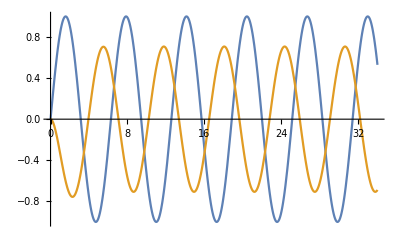

```mathematica
{RVal,CVal}={1.0,1};
TMax=34;
V=Sin
qSol=NDSolveValue[{q[t]/CVal+RVal q'[t]+V[t]==0,q[0]==0},q,{t,0, TMax}];
Plot[{V[t],qSol[t]/CVal},{t,0, TMax}]
```

```mathematica
SawtoothWave
```

SawtoothWave

```mathematica
Information[SawtoothWave]
```

## LRC Circuit

SquareWave

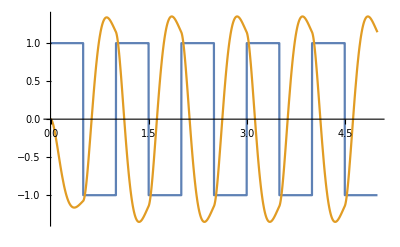

```mathematica
{RVal,CVal,LVal}={1.0,0.1,0.1};
TMax=5;
V=SquareWave
qSol=NDSolveValue[{q[t]/CVal+RVal q'[t]+LVal q''[t]+V[t]==0,q'[0]==0,q[0]==0},q,{t,0, TMax}];
Plot[{V[t],qSol[t]/CVal},{t,0, TMax}]
```